# Bondi Infall

## Bondi Solution

Start with HD solution, then add magnetic field.
Solve the following equations:
     f_1=Ṁ-4 πρur^2=0
f_2=Q̇ - h^2(1-(2M)/r+u^2)
Where Ṁ is the mass flux through any given sphere,
  and Q̇≡(h_∞)^2 is a measure of the heat flow.
  
  For reference, defaults in GRHydro_InitData are
     Ṁ=12.566370614359172954
      r_S=8
      r_min=10^-15
      r_max=400
      M_BH=1

#### Free parameters

```mathematica
mdot=10^-8;
mBH=1;
rSonic=SetPrecision[9,20];
Γ=5/3;

rmin=2;
rmax=400;
Npts=2000;
```

#### “Boundary” Data -- the Sonic Point

```mathematica
aSonic=SetPrecision[Sqrt[mBH/(2 rSonic - 3 mBH)],20];
vSonic=SetPrecision[Sqrt[mBH/(2 rSonic)],20];
ρSonic=SetPrecision[mdot/(4 π vSonic   rSonic^2),20];
hSonic =SetPrecision[ 1/(1 - (aSonic^2)/(Γ-1)),20];
Qdot = SetPrecision[hSonic^2 (1-3 vSonic^2),20];
κ= SetPrecision[ (hSonic aSonic^2)/(Γ ρSonic^(Γ-1)),20];
dr=SetPrecision[(rmax-rmin)/Npts,20];
```

#### Solve (Schwarzschild) -- Create a list using NSolve

```mathematica
h=SetPrecision[1+(Γ/(Γ-1)) κ ρ^(Γ-1),20];
evalQdot[ρ_,r_]=SetPrecision[(1+(Γ/(Γ-1)) κ ρ^(Γ-1))^2  (1 - (2mBH)/r+(mdot/(4 π ρ r^2))^2),20];
evalfQdot[ρ_,r_]=SetPrecision[Qdot-evalQdot[ρ,r],20];
evalfMdot[ρ_,u_,r_]=SetPrecision[u-mdot/(4 π ρ r^2),20];
tolSys=10^-20;
syseqns = {mdot - 4 π ρ u r^2==0,
                Qdot - h^2 (1 - (2 mBH)/r + u^2)==0};
eqnQdot={evalfQdot[ρ,r]==0, evalfMdot[ρ,u,r]==0};
```

```mathematica
rSchwarz=Table[SetPrecision[rmin*10^(i N[(Log[10,rmax]-Log[10,rmin])/(Npts-1)]) ,20],{i,Npts-1}];
solSchwarz=Table[ FindInstance[ eqnQdot/.{r->rs},{ρ,u},Reals,2,WorkingPrecision->20],{rs,rSchwarz}];
```

#### Change of coordinates and other derived ID

```mathematica
v= -u/Sqrt[1-(2 mBH)/r+u^2];
accretion:=4 π ρ u r^2;
enthalpyInf2:=h^2 (1-(2 mBH)/r+u^2);
rIso=Table[
   If[ rSchwarz⟦i⟧<2 mBH, 
             1/2( Sqrt[rSchwarz⟦i⟧^2-2 mBH rSchwarz⟦i⟧]+rSchwarz⟦i⟧-mBH),
            1/2( Sqrt[Abs[rSchwarz⟦i⟧^2-2 mBH rSchwarz⟦i⟧]]+rSchwarz⟦i⟧-mBH)], {i,Npts-1}];
a[ρ_]= (κ Γ ρ^(Γ-1))/(1-(κ Γ ρ^(Γ-1))/(Γ-1));
```

#### Plot the solutions as functions of rSchwarz, NDSolve

```mathematica
ρSchwarz=Table [ {  rSchwarz⟦i⟧,First[ρ/.solSchwarz⟦i⟧],Last[ρ/.solSchwarz⟦i⟧]},{i,Npts-1}];
uSchwarz=Table [ {  rSchwarz⟦i⟧,First[u/.solSchwarz⟦i⟧],Last[u/.solSchwarz⟦i⟧]},{i,Npts-1}];
vSchwarz=Table [ {  rSchwarz⟦i⟧,First[v/.solSchwarz⟦i⟧/.{r->rSchwarz⟦i⟧}],
                                      Last[v/.solSchwarz⟦i⟧/.{r->rSchwarz⟦i⟧}]},{i,Npts-1}];
vSchwarz=Table [ {  rSchwarz⟦i⟧,First[v/.solSchwarz⟦i⟧/.{r->rSchwarz⟦i⟧}],
                                      Last[v/.solSchwarz⟦i⟧/.{r->rSchwarz⟦i⟧}]},{i,Npts-1}];
MachNumSchwarz=Table[ {rSchwarz⟦i⟧,(uSchwarz⟦i⟧⟦2⟧)/a[ρSchwarz⟦i⟧⟦2⟧], (uSchwarz⟦i⟧⟦3⟧)/a[ρSchwarz⟦i⟧⟦3⟧]},{i,Npts-1}];
resMdotSchwarz=SetPrecision[Table [ {  rSchwarz⟦i⟧,First[((accretion/mdot-1)/.{r->rSchwarz⟦i⟧})/.solSchwarz⟦i⟧],Last[((accretion/mdot-1)/.{r->rSchwarz⟦i⟧})/.solSchwarz⟦i⟧]},{i,Npts-1}],20];
resQdotSchwarz=SetPrecision[Table [ {rSchwarz⟦i⟧,First[((enthalpyInf2/Qdot-1)/.{r->rSchwarz⟦i⟧})/.solSchwarz⟦i⟧],Last[((enthalpyInf2/Qdot-1)/.{r->rSchwarz⟦i⟧})/.solSchwarz⟦i⟧]},{i,Npts-1}],20];


xrange={2,30};
rangeU={ Min[ uSchwarz⟦All,{2,3}⟧], Max[ uSchwarz⟦All,{2,3}⟧ ] }
rangeρ={ Min[ ρSchwarz⟦All,{2,3}⟧], Max[ ρSchwarz⟦All,{2,3}⟧ ] }
rangeV={ Min[ vSchwarz⟦All,{2,3}⟧], Max[ vSchwarz⟦All,{2,3}⟧ ] }
rangeA = { Min[ MachNumSchwarz⟦All,{2,3}⟧], Max[ MachNumSchwarz⟦All,{2,3}⟧]}
```

{0.002021564814845569,0.7292693242911504}

{2.777520691050461×10^-14,9.09849617006074×10^-8}

{-0.997520715191253,-0.002026633596415351}

{-0.03718436354581751,316.5927963369275}

```mathematica
finalSolution=Table[  Flatten[{rSchwarz⟦i⟧, rIso⟦i⟧, 
                                                                  If[ rSchwarz⟦i⟧≤ rSonic,ρSchwarz⟦i,2⟧,ρSchwarz⟦i,3⟧], 
                                                                  If[ rSchwarz⟦i⟧≤ rSonic,uSchwarz⟦i,2⟧,uSchwarz⟦i,3⟧], 
                                                                  If[ rSchwarz⟦i⟧≤ rSonic,vSchwarz⟦i,2⟧,vSchwarz⟦i,3⟧], 
						 If[rSchwarz⟦i⟧≤rSonic, uSchwarz⟦i,2⟧/((1-(mBH/(2 rIso⟦i⟧))^2) √(1+(1+mBH/(2 rIso⟦i⟧))^4 uSchwarz⟦i,2⟧^2)),                     uSchwarz⟦i,3⟧/((1-(mBH/(2 rIso⟦i⟧))^2) √(1+(1+mBH/(2 rIso⟦i⟧))^4 uSchwarz⟦i,3⟧^2))],
                                                                        If[ rSchwarz⟦i⟧≤ rSonic,MachNumSchwarz⟦i,2⟧,MachNumSchwarz⟦i,3⟧],
If[ rSchwarz⟦i⟧≤ rSonic,resMdotSchwarz⟦i,2⟧,resMdotSchwarz⟦i,3⟧],
If[ rSchwarz⟦i⟧≤ rSonic,resQdotSchwarz⟦i,2⟧,resQdotSchwarz⟦i,3⟧]}
                                          ],{i,Npts-1}];
fullSolution=Table[ Flatten[ {rSchwarz⟦i⟧, rIso⟦i⟧,ρSchwarz⟦i,{2,3}⟧,uSchwarz⟦i,{2,3}⟧}],{i,Npts-1}];
```

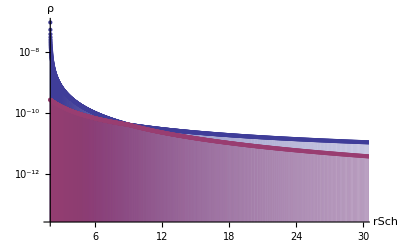

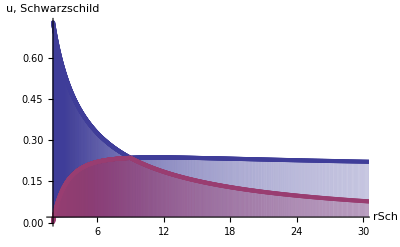

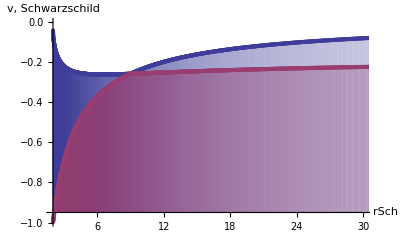

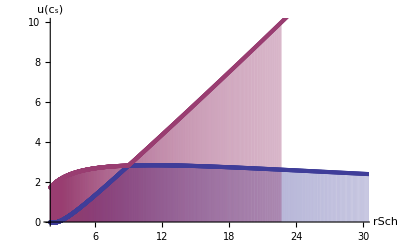

```mathematica
ListLogPlot[ {ρSchwarz⟦All,{1,3}⟧,ρSchwarz⟦All,{1,2}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,rangeρ},AxesLabel->{"rSch","ρ"}]
ListPlot[{uSchwarz⟦All,{1,2}⟧,uSchwarz⟦All,{1,3}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,rangeU},AxesLabel->{"rSch","u, Schwarzschild"}]
ListPlot[{vSchwarz⟦All,{1,3}⟧,vSchwarz⟦All,{1,2}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,rangeV},AxesLabel->{"rSch","v, Schwarzschild"}]
ListPlot[{MachNumSchwarz⟦All,{1,3}⟧,MachNumSchwarz⟦All,{1,2}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,{0,10}},AxesLabel->{"rSch","u(c_s)"} ]
```

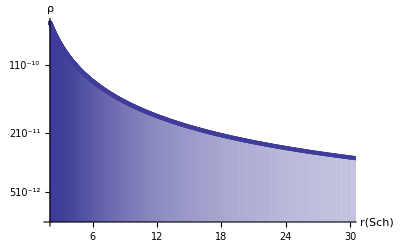

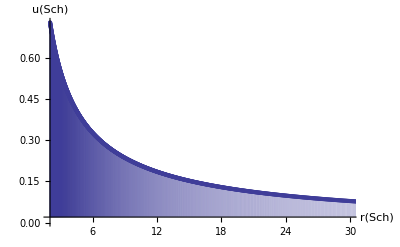

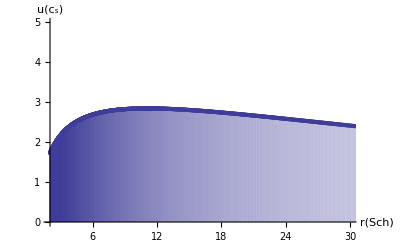

```mathematica
ListLogPlot[{finalSolution⟦All,{1,3}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,{0,10}},AxesLabel->{"r(Sch)","ρ"} ]
ListPlot[{finalSolution⟦All,{1,4}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,rangeU},AxesLabel->{"r(Sch)","u(Sch)"} ]
ListPlot[{finalSolution⟦All,{1,7}⟧},Filling->Axis,PlotStyle->Automatic,PlotRange->{xrange,{0,5}},AxesLabel->{"r(Sch)","u(c_s)"} ]
```

#### Residuals given solution (in Schwarzschild)

```mathematica
Max[ SetPrecision[Abs[   resMdotSchwarz⟦All,2⟧  ],20]]
Max[ SetPrecision[Abs[   resQdotSchwarz⟦All,2⟧  ],20]]
```

0

0

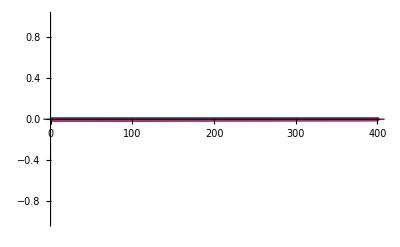

-Graphics-

```mathematica
ListPlot[{resMdotSchwarz⟦All,{1,2}⟧,resMdotSchwarz⟦All,{1,3}⟧},Filling->Axis,PlotStyle->Automatic]
ListPlot[{resQdotSchwarz⟦All,{1,2}⟧,resQdotSchwarz⟦All,{1,3}⟧},Filling->Axis,PlotStyle->Automatic]
```

#### Write out current solution, only the desired solution branches (v/a decreases with r, no over-suppression of inflow near horizon)

```mathematica
headerlines={ "# Bondi solution given the following parameters:",
		       "#     r_sonic = "<>ToString[N[rSonic]],
		       "#     mdot = "<>ToString[N[mdot],InputForm],
                             "#     M_BH = "<>ToString[N[mBH],InputForm],
                             "#     r_range = "<>ToString[N[{rmin,rmax}],InputForm],
			"#",
		    "# 1:r(Iso) 2:r(Sch) 3:rho 4:u(Sch) 5:v(Sch) 6:v(Iso) 7:MachNum 8:delta(Mdot) 9:delta(Qdot)"
};
foutbase=Directory[]<>"Data/Runs/ETMHD/BondiSolution_rs_"<>ToString[N[rSonic]]<>"_mdot_"<>ToString[ScientificForm[N[mdot],NumberFormat->(Row[{#1,"e",#3}]&)]];
foutbase=Directory[]<>"/BondiSolution_rs_"<>ToString[N[rSonic]]<>"_mdot_"<>ToString[ScientificForm[N[mdot],NumberFormat->(Row[{#1,"e",#3}]&)]]
```

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolution_rs_9._mdot_1.e-8

```mathematica
Export[ foutbase<>".dat",finalSolution]
Export[foutbase<>".txt",headerlines]
```

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolution_rs_9._mdot_1.e-8.dat

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolution_rs_9._mdot_1.e-8.txt

#### Write out both solutions,

```mathematica
headerlines={ "# Bondi solution given the following parameters:",
		       "#     r_sonic = "<>ToString[N[rSonic]],
		       "#     mdot = "<>ToString[N[mdot],InputForm],
                             "#     M_BH = "<>ToString[N[mBH],InputForm],
                             "#     r_range = "<>ToString[N[{rmin,rmax}],InputForm],
			"#",
		    "# 1:r(Iso) 2:r(Sch) 3:rho1 4:rho2 5:u1 6:u2"
};
foutbase=Directory[]<>"Data/Runs/ETMHD/BondiSolutionFull_rs_"<>ToString[N[rSonic]]<>"_mdot_"<>ToString[ScientificForm[N[mdot],NumberFormat->(Row[{#1,"e",#3}]&)]];
foutbase=Directory[]<>"/BondiSolutionFull_rs_"<>ToString[N[rSonic]]<>"_mdot_"<>ToString[ScientificForm[N[mdot],NumberFormat->(Row[{#1,"e",#3}]&)]]
```

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolutionFull_rs_9._mdot_1.e-8

```mathematica
Export[foutbase<>".dat",fullSolution]
Export[foutbase<>".txt",headerlines]
```

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolutionFull_rs_9._mdot_1.e-8.dat

/export/home/tbode6/CactusTrees/Maya_Lovelace/repos/GTThorns/SphericalInfall/doc/BondiSolutionFull_rs_9._mdot_1.e-8.txt